```mathematica
𝒟=0.05;
```

```mathematica
heqn=D[u[x,t], t]==𝒟 D[u[x,t], x,x];
```

```mathematica
ic=u[x,0]==Sin[π x];
```

```mathematica
bcx0=u[0,t]==0;
```

```mathematica
bcx1=u[1,t]==0;
```

```mathematica
ψ=NDSolve[{heqn,ic,bcx0,bcx1},u,{x,0,1},{t,0,1}]
```

{{u→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]}}

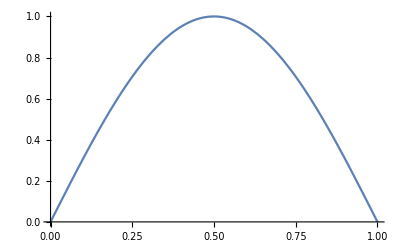

```mathematica
Plot[Evaluate[u[x,0]/.ψ],{x,0,1},PlotRange->All]
```

```mathematica
Animate[Plot[Evaluate[u[x,t]/.ψ],{x,0,1},PlotRange->{0,1}],{t,0,1,0.01}]
```